Given a detector with area A, a square subarray with edge length s, and σ is the probability density of lengths of cosmic rays, what is the chance that a cosmic ray will hit the subarray given that it has hit the detector?

This is similar to Buffon's needle in probability theory.  We assume that σ is discrete.  The probability is given by:

```mathematica
P[A_,s_,σ_,{l_,u_}]:=∑_(x=l)^u ρ[x,A,s] σ[x]
```

Here ρ gives the probability that a cosmic ray of length x will fall in the subarray.  Bounds are given by l and u and are supplied by the user.  We may break ρ up into (1) the probability that a given cosmic ray will be in reach the subarray regardless of orientation and (2) the likelihood it will hit the subarray given that it is possible to be detected.  Hence:

```mathematica
ρ[x_,A_,s_]:=ρ1[x,A,s] ρ2[x,s]
```

Here is a depiction of the area where it is possible to detect a cosmic ray:

-Graphics-

The total area is:

s^2+4 s x+π x^2

From this we may infer ρ1:

```mathematica
ρ1[x_,A_,s_]:=Min[(s^2+4 s x+π x^2)/A,1]
```

To calculate ρ2, we can observe that the problem does not depend on scale; the chance that a 2cm cosmic ray will hit a subarray with edge length 4cm is the same as the case of a 1cm cosmic ray and a subarray with edge length 2cm.  Since scale doesn't matter we rescale ρ2 to the situation where s=1:

```mathematica
ρ2[x_,s_]:=γ[x/s]
```

We calculate γ[r] via a Monty-Carlo simulation using python.  Below we perform a nonlinear regression:

```mathematica
gammamc=Import["gammamc.tsv"];
```

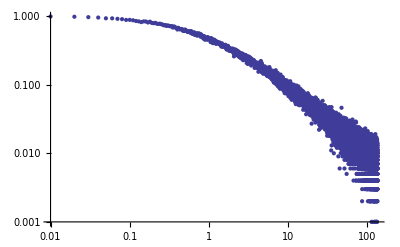

```mathematica
p1=ListLogLogPlot[gammamc,PlotRange->All]
```

```mathematica
Fit[gammamc,{1/(r+1)},{r}]
```

0.952329/(1+r)

```mathematica
p2=LogLogPlot[0.952328518790203/(r+1),{r,0.01,100},PlotStyle->{Thick, Red},PlotRange->All];p3=LogLogPlot[1/(r+1),{r,0.01,100},PlotStyle->{Thick, Green},PlotRange->All];
```

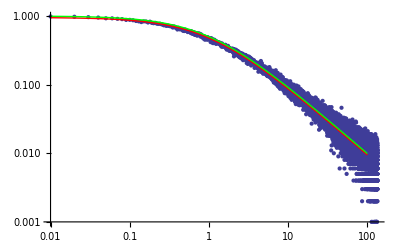

```mathematica
Show[p1,p2,p3]
```

We can see from the above graph that a least squares fit basically matches γ[r]=1/(r+1) for all intents and purposes.  Since this expression is elegant, we suspect it is the analytic solution to this problem:

```mathematica
γ[r_]:=1/(r+1)
```